```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

```mathematica
r0=1000;
k=N[3*(Log[2]+Log[5])/64];
r[t_]:=r0 Exp[-k t];
Nt[t_]:=r0 t+((r0/k)*(Exp[-k t]-1));
m[s_]:=NIntegrate[Nt[x],{x,0,s}];
pr[n_,t_]:=(Nt[t])^n/((n)!)Exp[-Nt[t]];
p1[n_]:=pr[n,10^-6]
p2[t_]:=pr[2,t/10^-6]
```

## p1(n)=probability that n events happen in time-t=1μs p2(t)=probability that 2 events happen in time-Δt

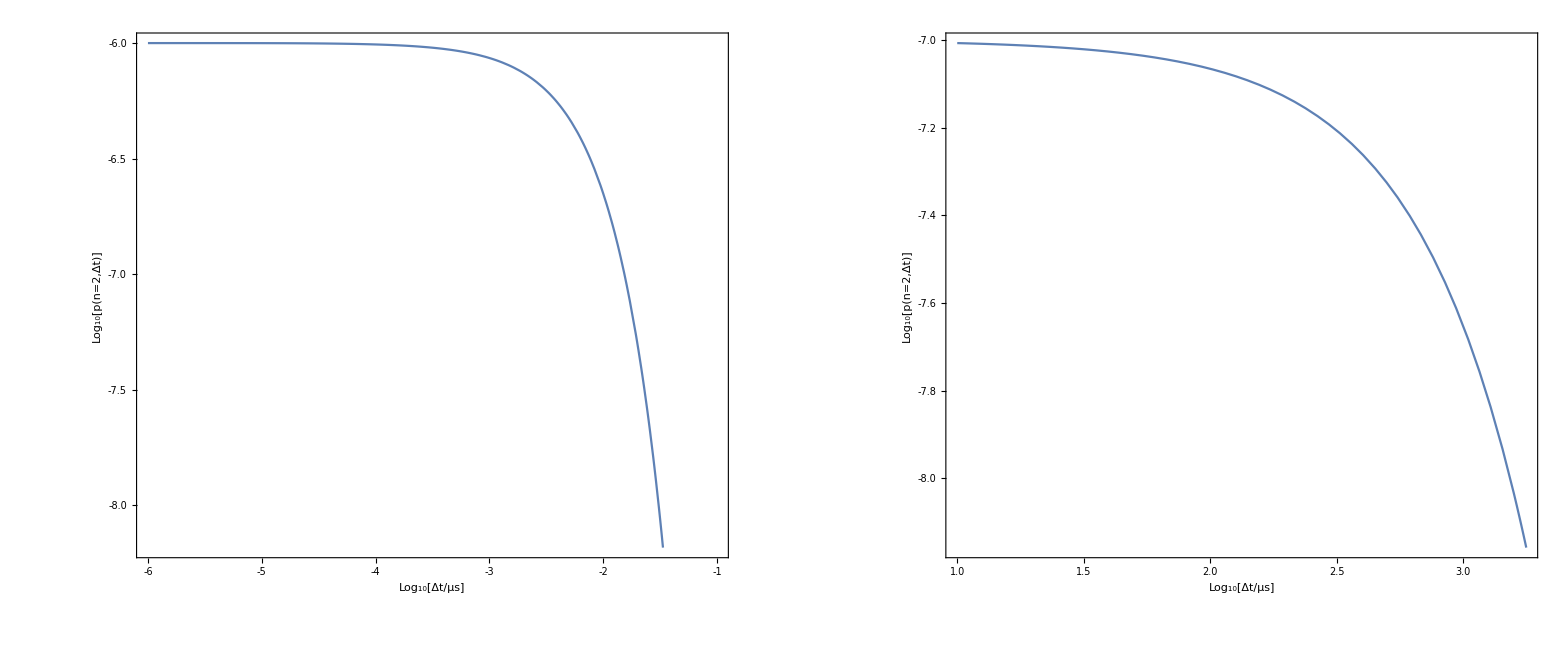

```mathematica
GraphicsGrid[{{Plot[(Log10[p2[10^y]]*1.5/10^7)-6,{y,-6,-1},Frame->True,FrameLabel->{"Log_10[Δt/μs]","Log_10[p(n=2,Δt)]"},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->1000],
Plot[(Log10[p2[10^y]]*1.5/10^12)-7,{y,1,3.25},Frame->True,FrameLabel->{"Log_10[Δt/μs]","Log_10[p(n=2,Δt)]"},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->1000]}},PlotLabel->"Probability of 2 UCN counts arriving within Δt"]
```

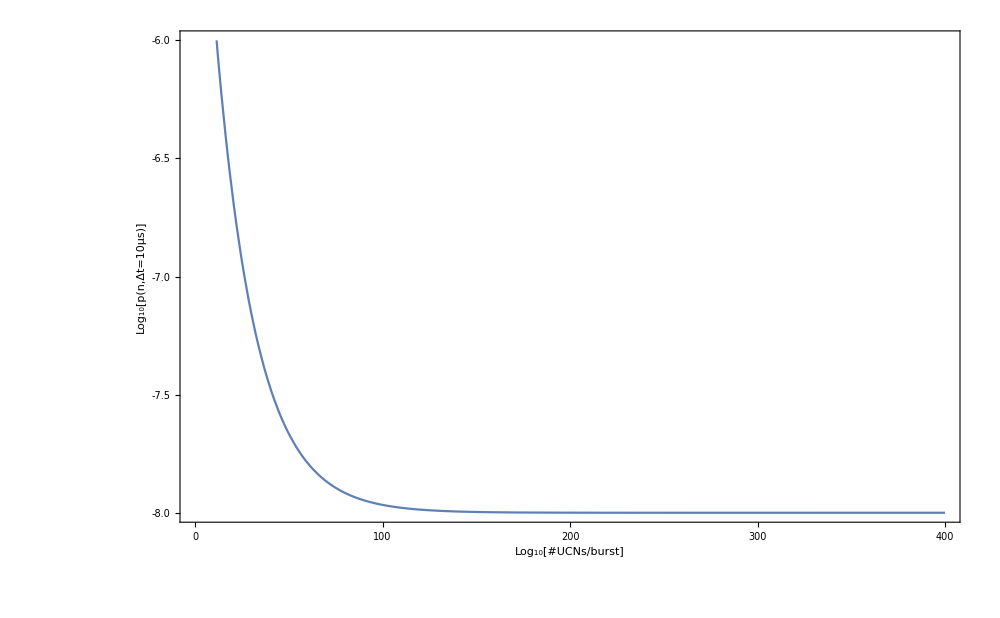

```mathematica
Plot[(-Log10[p1[10^(-y 2/100)]]/3)-8,{y,0,400},Frame->True,FrameLabel->{"Log_10[#UCNs/burst]","Log_10[p(n,Δt=10μs)]"},PlotRange->{{0,400},{-8,-6}},TicksStyle->Directive[FontSize->40],FrameTicks->LinTicks,LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->1000]
```

```mathematica
p1[n]
p2[t]
Simplify[p1[n]]
Simplify[p2[t]]
FullSimplify[p1[n]]
FullSimplify[p2[t]]
```

(5.07623265734364×10^-432 1000.^(-1+n))/((-1+n)!)

(ⅇ^(-(9264.95-9264.95 ⅇ^(-107934. t))/(1000000 t)-107934. t) (9264.95-9264.95 ⅇ^(-107934. t)))/(1000 t)

(5.07623293165873×10^-435 1000.^n)/((-1+n)!)

(ⅇ^((-0.00926495+0.00926495 ⅇ^(-107934. t)-215867. t^2)/t) (-9.26495+9.26495 ⅇ^(107934. t)))/t

(5.07623293165873×10^-435 1000.^n)/Gamma[n]

(ⅇ^((-0.00926495+0.00926495 ⅇ^(-107934. t)-215867. t^2)/t) (-9.26495+9.26495 ⅇ^(107934. t)))/t